```mathematica
MultiwayTagSystem[rule_,init_,t_]:=NestGraph[rule,init,t,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

```mathematica
MultiwayTagSystem[ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}}],
{{1,1}},
10
]
```

```mathematica
Table[
lFn[][[1]][[1]]
,{t,1,5}]/.{{{{{x_}}}}}->x
```

Part::partw: Part 1 of lFn[] does not exist.

{lFn[],lFn[],lFn[],lFn[],lFn[]}

```mathematica
lFn[8,8,8,8,3,8,3,5][[1]][[1]]
```

{3,4,5,6,9,12}

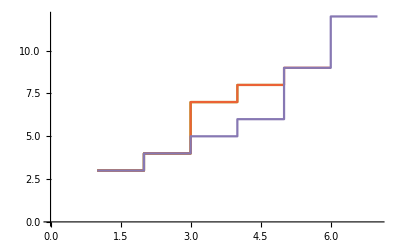

```mathematica
ListStepPlot[
{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}
]
```

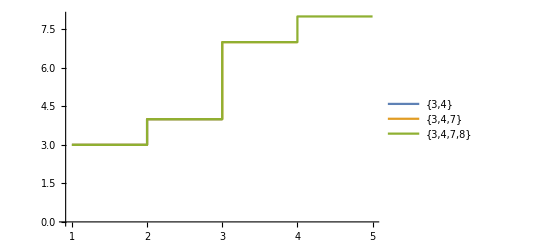

```mathematica
ListStepPlot[
{
Legended[
{3,4},
{3,4}
],
Legended[
{3,4,7},
{3,4,7}
]
,Legended[
{3,4,7,8},
{3,4,7,8}
]
}
]
```

```mathematica
PrimePi[Range[20]]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8}

```mathematica
Table[
{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}[[i]],
{
i,
1,
Length[{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}]
}
]
```

{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}

```mathematica
Map[Legended[#,#]&,{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}]
```

{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
,allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
},
(*Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]*)
 (*Length /@allPaths[[-1]]*)
Table[
Length /@FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
]]]

lFn[l_,k_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]

(*ListStepPlot[Table[
lFn[k,l,t][[1]][[1]]
,{t,1,15},
{k,1,2^l},
{l,2,3}]/.{{{{{x_}}}}} -> x]*)
```

```mathematica
lFn[3,2,6][[1]][[1]]
```

{{2},{2,5},{2,5,4},{2,5,6},{2,5,4,5},{2,5,6,9},{2,5,4,5,4},{2,5,4,5,6},{2,5,4,5,8},{2,5,6,9,12},{2,5,4,5,4,7},{2,5,4,5,6,7},{2,5,4,5,8,9},{2,5,6,9,12,13},{2,5,4,5,6,7,6},{2,5,4,5,6,7,8},{2,5,4,5,4,7,10},{2,5,4,5,8,9,10},{2,5,6,9,12,13,14},{2,5,6,9,12,13,16}}

```mathematica
table = Table[
ListLinePlot3D[

MapIndexed[
Legended[#1,Tuples[{0,1},l][[k]]]&,lFn[k,l,t][[1]][[1]]
],
Filling->Axis,
Axes->{True,False,True},
ImageSize->Large,
PlotTheme->"Marketing"
]
,{l,2,3},
{k,1,2^l},{t,1,6}
]/.{{{x_}}}->x
```

Extract::partw: Part 2 of {Directive[color,AbsoluteThickness[2]]} does not exist.

Extract::partw: Part 2 of {{color,AbsoluteThickness[2]}} does not exist.

Extract::partw: Part 3 of {Directive[color,AbsoluteThickness[2]]} does not exist.

General::stop: Further output of Extract::partw will be suppressed during this calculation.

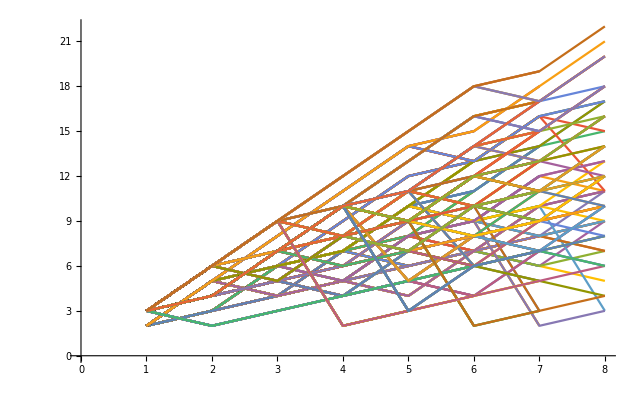

```mathematica
ListLinePlot[Flatten[Table[lFn[l,k,t][[1]][[1]],{l,2,3},{k,1,2^l},{t,1,7}],3]]
```

```mathematica
lFn[3,1,3][[1]][[1]]
```

{{3},{3,2},{3,4},{3,4,5},{3,4,5,6}}

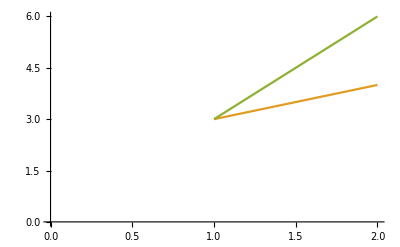
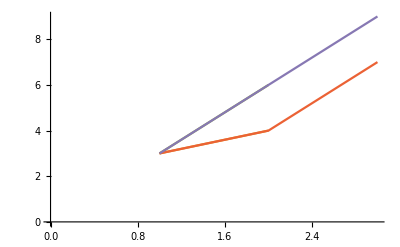
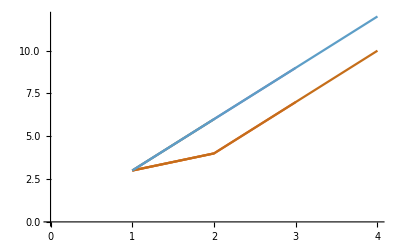
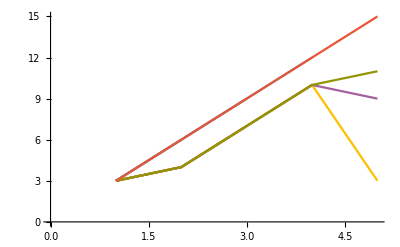
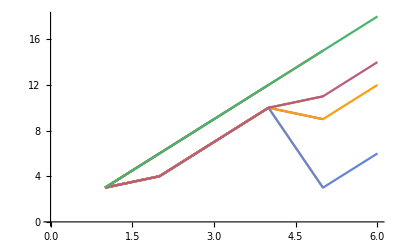
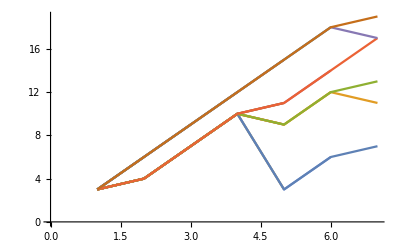
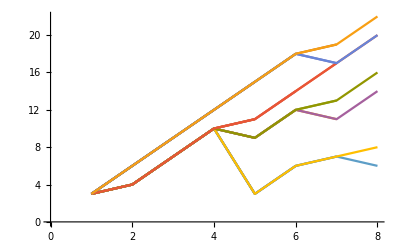

{{3},{3,4},{3,6},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3,4,7,10},{3,6,9,12},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3,4,7,10},{3,6,9,12},{3,4,7,10,3},{3,4,7,10,9},{3,4,7,10,11},{3,6,9,12,15},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3,4,7,10},{3,6,9,12},{3,4,7,10,3},{3,4,7,10,9},{3,4,7,10,11},{3,6,9,12,15},{3,4,7,10,3,6},{3,4,7,10,9,12},{3,4,7,10,11,14},{3,6,9,12,15,18},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3,4,7,10},{3,6,9,12},{3,4,7,10,3},{3,4,7,10,9},{3,4,7,10,11},{3,6,9,12,15},{3,4,7,10,3,6},{3,4,7,10,9,12},{3,4,7,10,11,14},{3,6,9,12,15,18},{3,4,7,10,3,6,7},{3,4,7,10,9,12,11},{3,4,7,10,9,12,13},{3,4,7,10,11,14,17},{3,6,9,12,15,18,17},{3,6,9,12,15,18,19},{3},{3,4},{3,6},{3,4,7},{3,6,9},{3,4,7,10},{3,6,9,12},{3,4,7,10,3},{3,4,7,10,9},{3,4,7,10,11},{3,6,9,12,15},{3,4,7,10,3,6},{3,4,7,10,9,12},{3,4,7,10,11,14},{3,6,9,12,15,18},{3,4,7,10,3,6,7},{3,4,7,10,9,12,11},{3,4,7,10,9,12,13},{3,4,7,10,11,14,17},{3,6,9,12,15,18,17},{3,6,9,12,15,18,19},{3,4,7,10,3,6,7,6},{3,4,7,10,3,6,7,8},{3,4,7,10,9,12,11,14},{3,4,7,10,9,12,13,16},{3,4,7,10,11,14,17,20},{3,6,9,12,15,18,17,20},{3,6,9,12,15,18,19,22}}

```mathematica
Table[ListLinePlot[
lFn[lengthInitialCondition,
indexInitialConditionWithGivenLength,
timeStep][[1]][[1]]],
{lengthInitialCondition,3,3},
{indexInitialConditionWithGivenLength,2^lengthInitialCondition,2^lengthInitialCondition},
{timeStep,1,7}]
```

```mathematica
ListLinePlot3D[

MapIndexed[
Legended[#1,Tuples[{0,1},l][[k]]]&,lFn[k,l,t][[1]][[1]]
],
Filling->Axis,
Axes->{True,False,True},
ImageSize->Large,
PlotTheme->"Marketing"
]
```

```mathematica
lFn[3,
6,
3][[1]][[1]]
```

{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10}}

```mathematica
table1 = Table[
lFn[3,
6,
timeStep][[1]][[1]],
{timeStep,1,10}
]
```

{{{3},{3,6}},{{3},{3,6},{3,6,5},{3,6,7}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16},{3,6,7,10,9,2,3},{3,6,7,10,9,8,7},{3,6,7,10,9,8,9},{3,6,7,10,9,10,13},{3,6,5,8,9,12,13},{3,6,7,10,13,16,17}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16},{3,6,7,10,9,2,3},{3,6,7,10,9,8,7},{3,6,7,10,9,8,9},{3,6,7,10,9,10,13},{3,6,5,8,9,12,13},{3,6,7,10,13,16,17},{3,6,7,10,9,2,3,4},{3,6,7,10,9,8,7,10},{3,6,7,10,9,8,9,12},{3,6,5,8,9,12,13,12},{3,6,5,8,9,12,13,14},{3,6,7,10,9,10,13,16},{3,6,7,10,13,16,17,18},{3,6,7,10,13,16,17,20}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16},{3,6,7,10,9,2,3},{3,6,7,10,9,8,7},{3,6,7,10,9,8,9},{3,6,7,10,9,10,13},{3,6,5,8,9,12,13},{3,6,7,10,13,16,17},{3,6,7,10,9,2,3,4},{3,6,7,10,9,8,7,10},{3,6,7,10,9,8,9,12},{3,6,5,8,9,12,13,12},{3,6,5,8,9,12,13,14},{3,6,7,10,9,10,13,16},{3,6,7,10,13,16,17,18},{3,6,7,10,13,16,17,20},{3,6,7,10,9,2,3,4,5},{3,6,7,10,9,8,7,10,11},{3,6,5,8,9,12,13,12,13},{3,6,7,10,9,8,9,12,11},{3,6,7,10,9,8,9,12,15},{3,6,5,8,9,12,13,14,13},{3,6,5,8,9,12,13,14,17},{3,6,7,10,9,10,13,16,15},{3,6,7,10,9,10,13,16,17},{3,6,7,10,13,16,17,18,21},{3,6,7,10,13,16,17,20,15},{3,6,7,10,13,16,17,20,21}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16},{3,6,7,10,9,2,3},{3,6,7,10,9,8,7},{3,6,7,10,9,8,9},{3,6,7,10,9,10,13},{3,6,5,8,9,12,13},{3,6,7,10,13,16,17},{3,6,7,10,9,2,3,4},{3,6,7,10,9,8,7,10},{3,6,7,10,9,8,9,12},{3,6,5,8,9,12,13,12},{3,6,5,8,9,12,13,14},{3,6,7,10,9,10,13,16},{3,6,7,10,13,16,17,18},{3,6,7,10,13,16,17,20},{3,6,7,10,9,2,3,4,5},{3,6,7,10,9,8,7,10,11},{3,6,5,8,9,12,13,12,13},{3,6,7,10,9,8,9,12,11},{3,6,7,10,9,8,9,12,15},{3,6,5,8,9,12,13,14,13},{3,6,5,8,9,12,13,14,17},{3,6,7,10,9,10,13,16,15},{3,6,7,10,9,10,13,16,17},{3,6,7,10,13,16,17,18,21},{3,6,7,10,13,16,17,20,15},{3,6,7,10,13,16,17,20,21},{3,6,7,10,9,2,3,4,5,6},{3,6,7,10,9,8,9,12,11,12},{3,6,7,10,9,8,7,10,11,14},{3,6,5,8,9,12,13,14,13,12},{3,6,5,8,9,12,13,14,13,14},{3,6,5,8,9,12,13,12,13,14},{3,6,5,8,9,12,13,12,13,16},{3,6,7,10,9,8,9,12,15,18},{3,6,7,10,9,10,13,16,15,18},{3,6,7,10,13,16,17,20,15,18},{3,6,5,8,9,12,13,14,17,20},{3,6,7,10,9,10,13,16,17,20},{3,6,7,10,13,16,17,20,21,20},{3,6,7,10,13,16,17,20,21,22},{3,6,7,10,13,16,17,18,21,24}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16},{3,6,7,10,9,2,3},{3,6,7,10,9,8,7},{3,6,7,10,9,8,9},{3,6,7,10,9,10,13},{3,6,5,8,9,12,13},{3,6,7,10,13,16,17},{3,6,7,10,9,2,3,4},{3,6,7,10,9,8,7,10},{3,6,7,10,9,8,9,12},{3,6,5,8,9,12,13,12},{3,6,5,8,9,12,13,14},{3,6,7,10,9,10,13,16},{3,6,7,10,13,16,17,18},{3,6,7,10,13,16,17,20},{3,6,7,10,9,2,3,4,5},{3,6,7,10,9,8,7,10,11},{3,6,5,8,9,12,13,12,13},{3,6,7,10,9,8,9,12,11},{3,6,7,10,9,8,9,12,15},{3,6,5,8,9,12,13,14,13},{3,6,5,8,9,12,13,14,17},{3,6,7,10,9,10,13,16,15},{3,6,7,10,9,10,13,16,17},{3,6,7,10,13,16,17,18,21},{3,6,7,10,13,16,17,20,15},{3,6,7,10,13,16,17,20,21},{3,6,7,10,9,2,3,4,5,6},{3,6,7,10,9,8,9,12,11,12},{3,6,7,10,9,8,7,10,11,14},{3,6,5,8,9,12,13,14,13,12},{3,6,5,8,9,12,13,14,13,14},{3,6,5,8,9,12,13,12,13,14},{3,6,5,8,9,12,13,12,13,16},{3,6,7,10,9,8,9,12,15,18},{3,6,7,10,9,10,13,16,15,18},{3,6,7,10,13,16,17,20,15,18},{3,6,5,8,9,12,13,14,17,20},{3,6,7,10,9,10,13,16,17,20},{3,6,7,10,13,16,17,20,21,20},{3,6,7,10,13,16,17,20,21,22},{3,6,7,10,13,16,17,18,21,24},{3,6,7,10,9,2,3,4,5,6,7},{3,6,7,10,9,8,9,12,11,12,13},{3,6,5,8,9,12,13,14,13,12,13},{3,6,7,10,9,8,7,10,11,14,15},{3,6,5,8,9,12,13,12,13,14,13},{3,6,5,8,9,12,13,12,13,14,17},{3,6,5,8,9,12,13,14,13,14,13},{3,6,5,8,9,12,13,14,13,14,17},{3,6,5,8,9,12,13,12,13,16,17},{3,6,7,10,9,8,9,12,15,18,19},{3,6,7,10,9,10,13,16,15,18,19},{3,6,7,10,13,16,17,20,15,18,17},{3,6,7,10,13,16,17,20,15,18,19},{3,6,5,8,9,12,13,14,17,20,21},{3,6,7,10,13,16,17,20,21,20,19},{3,6,7,10,13,16,17,20,21,20,21},{3,6,7,10,9,10,13,16,17,20,19},{3,6,7,10,9,10,13,16,17,20,23},{3,6,7,10,13,16,17,20,21,22,25},{3,6,7,10,13,16,17,18,21,24,23},{3,6,7,10,13,16,17,18,21,24,25}}}

10

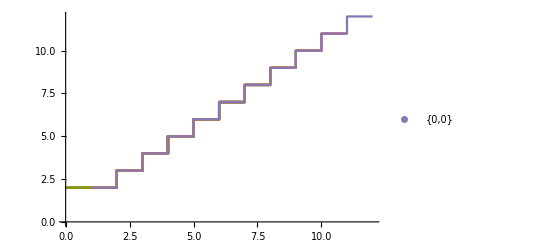
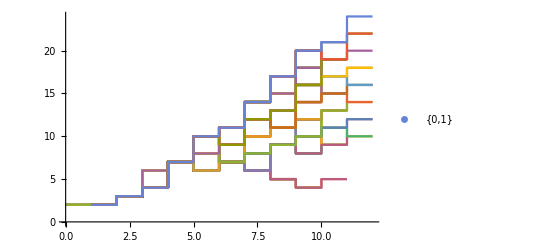
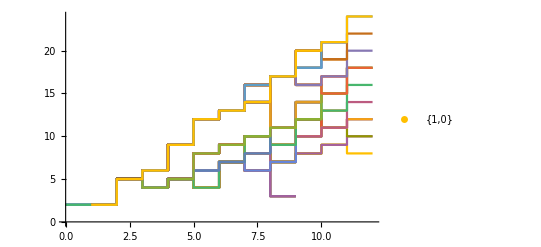
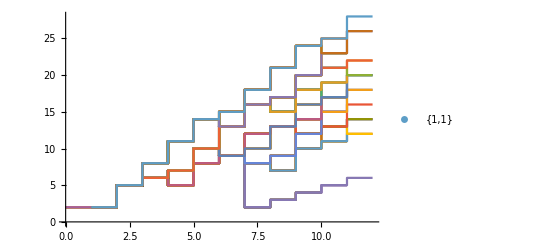
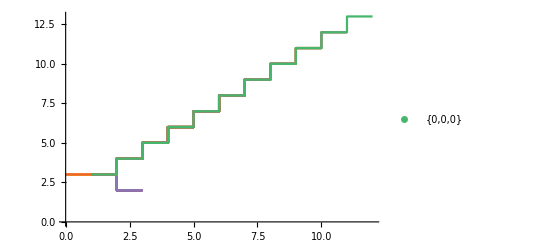
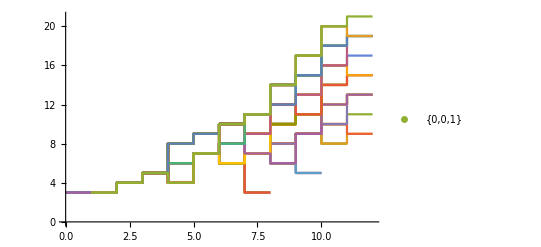
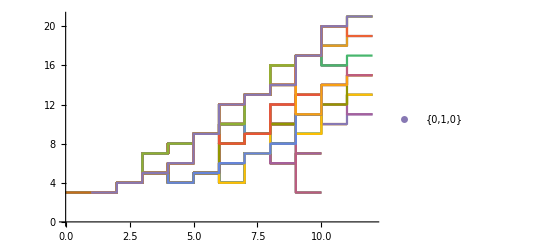
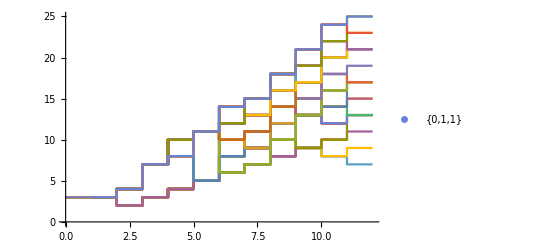

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
,allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
},
(*Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]*)
 (*Length /@allPaths[[-1]]*)
Table[
Length /@FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
]]]
lFn[l_,k_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
Length[table1]
Table[ListStepPlot[Legended[FlattenAt[
 Table[
lFn[lengthInitialCondition,
indexInitialConditionWithGivenLength,
timeStep][[1]][[1]],
{timeStep,1,10}
]
,
{#}&/@Range[10]],Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]]],
{lengthInitialCondition,2,3},
{indexInitialConditionWithGivenLength,1,2^lengthInitialCondition}]
```

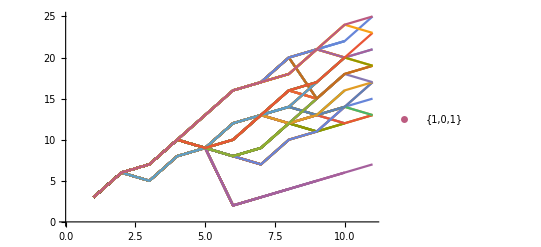

```mathematica
ListLinePlot[Legended[FlattenAt[table1,{#}&/@Range[Length[table1]]],Tuples[{0,1},3][[6]]]]
```

```mathematica
{#}&/@Range[5]
```

{{1},{2},{3},{4},{5}}

```mathematica
(*Flatten[table1,{{2},{1}}]*)
table1
FlattenAt[table1,{#}&/@Range[Length[table1]]]
```

{{{3},{3,6}},{{3},{3,6},{3,6,5},{3,6,7}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13}},{{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16}}}

{{3},{3,6},{3},{3,6},{3,6,5},{3,6,7},{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3},{3,6},{3,6,5},{3,6,7},{3,6,5,8},{3,6,7,10},{3,6,5,8,9},{3,6,7,10,9},{3,6,7,10,13},{3,6,7,10,9,2},{3,6,7,10,9,8},{3,6,7,10,9,10},{3,6,5,8,9,12},{3,6,7,10,13,16}}

```mathematica
lFn[3,2,6][[1]][[1]]
```

{{2},{2,5},{2,5,4},{2,5,6},{2,5,4,5},{2,5,6,9},{2,5,4,5,4},{2,5,4,5,6},{2,5,4,5,8},{2,5,6,9,12},{2,5,4,5,4,7},{2,5,4,5,6,7},{2,5,4,5,8,9},{2,5,6,9,12,13},{2,5,4,5,6,7,6},{2,5,4,5,6,7,8},{2,5,4,5,4,7,10},{2,5,4,5,8,9,10},{2,5,6,9,12,13,14},{2,5,6,9,12,13,16}}

```mathematica
lFn[2^3,3,10][[1]][[1]]
```

{3,6,9,12,15,18,19,22,25,28,29}

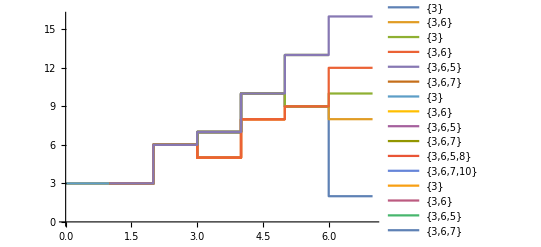

```mathematica
ListStepPlot[Map[Legended[#,#]&,FlattenAt[table1,{#}&/@Range[Length[table1]]]],]
```

```mathematica
Map[Legended[#,#]&,{{3,4},{3,4,7},{3,4,7,8},{3,4,7,8,9},{3,4,5,6,9,12}}]
```

```mathematica
table[[1]][[2^2]]
```

{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}

```mathematica
Tuples[{0,1},3][[2^3]]
```

{1,1,1}

```mathematica
table
```

{{{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}},{{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5},{3,4,7}}},{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,2,3},{3,4,7}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,5},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}}}

```mathematica
AllPathCanyonsBinary[table]
```

VertexList::graph: A graph object is expected at position 1 in VertexList[{{{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}},{{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},«4»,{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}}}].

General::stop: Further output of VertexList::graph will be suppressed during this calculation.

FindPath::graph: A graph object is expected at position 1 in «1».

FindShortestPath::graph: A graph object is expected at position 1 in FindShortestPath[{{{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}},{{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},«4»,{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}}},{{«1»},{«1»}},{{«1»},{«1»}}].

FindShortestPath::graph: A graph object is expected at position 1 in FindShortestPath[2,2,2].

{FindShortestPath[2,2,2]}

```mathematica
table
```

{{{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}},{{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5},{3,4,7}}},{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,2,3},{3,4,7}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,5},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}}}

```mathematica
{
{
{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}
},{
{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5},{3,4,7}}},{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,2,3},{3,4,7}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,5},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}
}
}
```

```mathematica
table
```

{{{{2,{2,3}},{2,{2,3},{2,3,4}}},{{2,{2,3}},{2,{2,3},{2,3,4},{2,3,6}}},{{2,{2,5}},{2,{2,5},{2,5,4},{2,5,6}}},{{2,{2,5}},{2,{2,5},{2,5,6},{2,5,8}}}},{{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5}}},{{3,{3,4}},{3,{3,4},{3,4,5},{3,4,7}}},{{3,{3,2},{3,4}},{3,{3,2},{3,4},{3,2,3},{3,4,7}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,5},{3,6,7}}},{{3,{3,6}},{3,{3,6},{3,6,9}}},{{3,{3,4},{3,6}},{3,{3,4},{3,6},{3,4,7},{3,6,9}}}}}

```mathematica
ListLinePlot3D[
MapIndexed[
Legended[#1,Tuples[{0,1},1][[#2]]]&,table[[1]][[1]]
],
Filling->Axis,
Axes->{True,False,True},
ImageSize->Large,
PlotTheme->"Marketing"
]
```

ListLinePlot3D::ldata: {{,{} is not a valid dataset or list of datasets.

General::stop: Further output of ListLinePlot3D::ldata will be suppressed during this calculation.

ListLinePlot3D[{{2,{2,3}},{2,{2,3},{2,3,4}}},Filling→Axis,Axes→{True,False,True},ImageSize→Large,PlotTheme→Marketing]

```mathematica
Table[
ListLinePlot3D[
MapIndexed[
Legended[#1,Tuples[{0,1},n2+1][[#2]]]&,table[[n]][[n2]]
],
Filling->Axis,
Axes->{True,False,True},
ImageSize->Large,
PlotTheme->"Marketing"
]
,{n,1,Length[table]},{n, 1, Length[table[n]]}]
```

Table::itraw: Raw object 1 cannot be used as an iterator.

Table[ListLinePlot3D[MapIndexed[#1&,table⟦n⟧⟦n2⟧],Filling→Axis,Axes→{True,False,True},ImageSize→Large,PlotTheme→Marketing],{1,2,Length[table]},{n2,2,Length[table[n]]}]

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
MapIndexed[Tuples[{0,1},3][[#2]]&,table[[2]]]/.{x_}->x
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
MapIndexed[#&,table]
```

{{{2,3,4,5,6,7,8,9,10,11,12},{2,3,4,7,10,9,12,11,14,15,6,7,6,7,8,9,8,7,8,9,10,9,6,9,12,13,14,17,20,21,24},{2,5,4,5,4,7,10,9,12,11,14,3,6,7,6,7,10,11,8,11,14,15,16,17,16,17,8,9,10,11,12,11,6,9,12,13,14,17,20,21,24},{2,5,8,11,14,13,16,15,18,17,8,9,10,13,16,17,18,21,24,25,28}},{{3,4,5,6,7,8,9,10,11,12,13},{3,4,5,4,7,10,9,12,11,14,3,6,7,6,7,8,9,10,11,10,11,10,11,8,11,14,15,14,17,20,21},{3,4,5,4,5,4,7,10,9,12,11,14,3,6,7,6,7,8,9,8,7,8,9,10,9,6,9,12,13,14,17,20,21},{3,4,7,8,11,14,15,18,21,24,25},{3,4,7,10,9,12,11,14,15,16,19,22,11,6,7,6,7,8,9,8,7,8,9,10,9,6,9,12,13,14,17,20,21,24,27},{3,6,5,8,9,10,13,16,17,18,21,24,25},{3,6,9,8,9,12,11,10,13,16,17,20,23,26,27},{3,6,9,12,15,18,19,22,25,28,29}}}

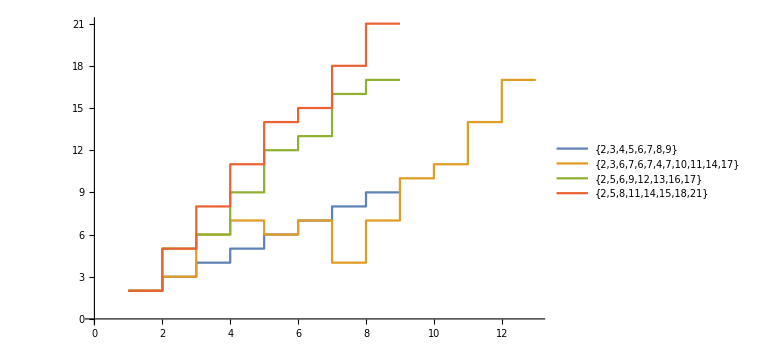
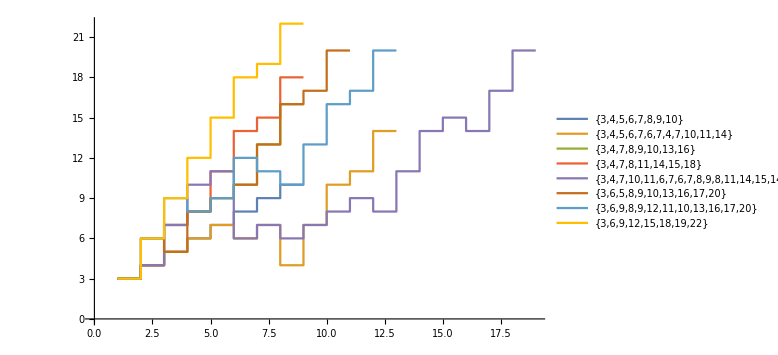

```mathematica
Table[ListStepPlot[
Map[Legended[#,#]&,table[[n]]], ImageSize->Large],{n,1,Length[table]}]
```